-Graphics-

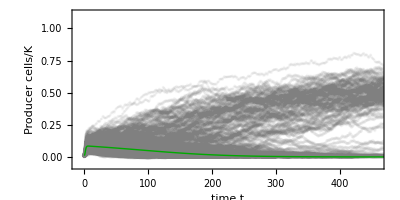

```mathematica
plotTrajectory[k_,o_]:=Module[
{length,t,c,d},
length=Length[data[[k]]]/3;
t=data[[k,1;;length]];
c = data[[k,length+1;;2length]];
d=data[[k,2length+1;;3length]];
ListPlot[Table[{t[[i]],c[[i]]/1000.},{i,1,length}]
,PlotStyle->Opacity[o,Gray]
,PlotRange->{{-10,460},{-70,1120}/1000.},
Frame->True,
FrameStyle->Directive[Thickness[0.0025],Black],
FrameTicksStyle->Opacity[1],FrameStyle->Opacity[1],
FrameLabel->{{"Producer cells/K",None},{"time t",None}},
LabelStyle->{FontSize->16,Black,FontFamily->"Arial"},
FrameTicks->{{All(*{{0,"0.0"},{200"0.2"}(*,{"0.4",400},{"0.6",600},{"0.8",800},{"1.0",1000}*)}*),None},{All,None}},
AspectRatio->0.5
,ImageSize->400
]
]

data = Import[NotebookDirectory[]<>"manytrajectories_C0_90_D0_10.txt","Table"];
dataODE = Import[NotebookDirectory[]<>"ODEtrajectory_C0_90_D0_10.txt","Table"];
Show[
plotTrajectory[#,0.025]&/@Range[1,200],
ListLinePlot[Table[{dataODE⟦l,1⟧,dataODE⟦l,2⟧/1000.},{l,1,dataODE//Length}],
PlotStyle->{Thick,Darker[Green]}]
]

data = Import[NotebookDirectory[]<>"manytrajectories_C0_10_D0_90.txt","Table"];
dataODE = Import[NotebookDirectory[]<>"ODEtrajectory_C0_10_D0_90.txt","Table"];
Show[plotTrajectory[#,0.035]&/@Range[1,200],
ListLinePlot[Table[{dataODE⟦l,1⟧,dataODE⟦l,2⟧/1000.},{l,1,dataODE//Length}],
PlotStyle->{Thick,Darker[Green]}
]
]
```

```mathematica
data = Import[NotebookDirectory[]<>"manytrajectories_C0_50_D0_50.txt","Table"];
dataODE = Import[NotebookDirectory[]<>"ODEtrajectory_C0_50_D0_50.txt","Table"];
Show[
plotTrajectory[#,0.035]&/@Range[1,200],
ListLinePlot[dataODE,
PlotStyle->Darker[Green]]
]
```

-Graphics-